```mathematica
ωrdef = {ωr -> Sqrt[(g/(4 R)) (1 - (mF hbar Ω)/(2 M g R)) Sqrt[1-ϵ^2]]};
ωzdef = {ωz -> 2 gF uB Bgrad /hbar Sqrt[(mF hbar)/(M Ω)] (1 - ϵ^2)^(3/4)};
Rdef = {R -> (ω hbar)/(2 gF uB Bgrad)};
ϵdef = {ϵ -> M g / (2 mF gF uB Bgrad)};
constants = {hbar ->  1.0546 10^-34, uB -> 9.274 10^-24, g-> 9.81, M -> 87 1.661 10^-27 , gF-> 1/2, bohrRad -> 5.30 10^-11};
setup = {Bgrad -> 50 0.01 1.17, ω-> 2 π 3 10^6 , mF -> 1};
```

Get RF dressing amplitude from measured trap frequencies. (in kHz)

```mathematica
(* Does not yet agree with matlab calcs *)
f = (Ω /.NSolve[(ωr /.ωrdef /. ϵdef /. Rdef /. constants /. setup) ==2 π 13, Ω])/2/π/10^3
(* Agrees with Matlab calcs *)
f = (Ω /.NSolve[(ωz /.ωzdef /. ϵdef /.Rdef/. constants /.setup) ==2 π 560, Ω])/2/π/10^3
```

{-51.2129}

{22.3298}

```mathematica
175*0.9*2
```

315.

What is the radial trap frequency for this value of Ω?

16626.9 √(1/f)

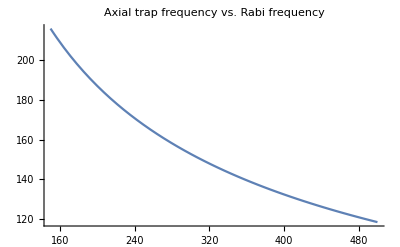

12.7927 √(1-0.000637843 f)

```mathematica
f=.
OmegaZ = (ωz/.ωzdef /. Ω -> 2 π f 10^3 /. Rdef /. ϵdef /. constants /. setup)
Plot[OmegaZ/ (2 π), {f, 150, 500}, PlotLabel-> "Axial trap frequency vs. Rabi frequency"]
fr = (ωr/ (2 π)/.ωrdef /. Ω -> 2 π f 10^3 /. Rdef /. ϵdef /. constants /. setup)
```

What is the variation in gravitational sag?

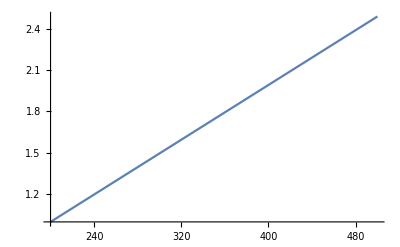

```mathematica
Plot[(g/OmegaZ^2/. constants ) /(6.45 10^-6), {f, 200, 500}]
```

## Chemical Potential

```mathematica
setup = {Bgrad -> 82.50 0.01, ω-> 2 π 3 10^6 , mF -> 1, Ω-> 2π 187 10^3};
ωGdef = {ωG-> (ωr ωr ωz)^(1/3) //. Join[ωrdef, ωzdef, constants, setup,Rdef, {ϵ-> 0}]};
Row[{"Geometric mean trap frequency, f_g = ", ωG / (2π), " Hz."}]
μdef = {μ -> 15^(2/5)/2 (N scatta/osca)^(2/5) hbar ωG};

(* Scattering length a *)
aDef = {osca ->  (hbar / (M ωG))^(1/2), scatta -> 100 bohrRad};

(* Chemical Potential - in Hz *)
chemPot = (μ )//. Join[ωGdef, μdef, setup, constants, aDef, {N -> 4 10^5}];
chemPot / (2 π hbar) /. constants
```

Geometric mean trap frequency, f_g = ωG/(2 π) Hz.

977.219

## Questions of lineshape

Define two functions: U(z), the potential energy as a function of z, and S(z), the separation between m_F^~=1 and m_F^~=0. The coordinate `z` here is taken such that z=0 corresponds to the resonance. Both are defined in terms of energy, so remember hbar when converting them to frequencies.

{z→-(ⅈ g hbar M Ω)/(Bgrad gF uB √(4 g^2 M^2-16 Bgrad^2 gF^2 uB^2))}

Minimum located at: -3.05359+0. ⅈ μm.

190295.

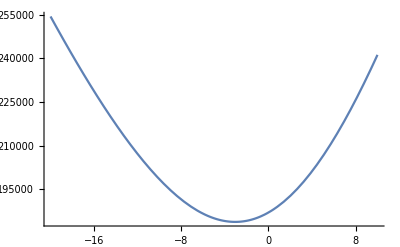

287.768

```mathematica
S[z_] := (hbar (Ω^2+δ^2)^(1/2))/. {δ -> gF uB (2 Bgrad z)/ (hbar)};
U[z_] := S[z] +M g z;
minZDef = Solve[D[U[z], z] == 0, z][[1]]
Row[{"Minimum located at: ", (10^6 z/.minZ) //. Join[constants, setup], " μm."}]
S[z/.minZDef]/(2 π hbar) //. Join[constants, setup]
Plot[U[z 10^-6]/(2 π hbar) //. Join[constants, setup], {z, -20, 10}]
ωz/ (2π) //.Join[ωzdef, constants, setup, Rdef, {ϵ-> 0}]
```

Expand the potential function as a power series and solve to determine the two values of z for which N’ = N/2, ie the FWHM of the rf resonance. These different Ns can be related through their chemical potentials, μ = μ0 0.5^(2/5).

```mathematica
s = Solve[U[z]-U[z/.minZDef]== μ0 (0.5)^(2/5), z];
zs = (z/.s) //. Join[constants, setup, {μ0-> 10^3 2 π hbar}];
Row[{"Resonant positions at ", 10^6 zs[[1]],",",10^6 zs[[2]],  " μm."}]
```

Resonant positions at -4.56449+0. ⅈ,-1.56787+0. ⅈ μm.

Once we have calculated these positions, we can determine the difference in splittings between them. Note that the below is simplified because both positions corresponding to the new chemical potential μ’s edges are below the z=0 point.

```mathematica
S[zs] /(2 π hbar) //. Join[constants, setup]
N@(S[zs[[2]]]-S[zs[[1]]])/(2 π hbar) //.Join[constants, setup]
```

{194285.+0. ⅈ,187874.+0. ⅈ}

-6410.95+0. ⅈ

Now use the solutions in z to determine the FWHM of the rf probe resonance. Convert the FWHM points from z coordinates to rf detunings.

```mathematica
δRF = ((δ /. δdef) / z) zs;
(δRF)//. Join[constants, setup]
```

{25661.6,4.85498×10^7}

### Same approach, but approximating the potential as harmonic

```mathematica
Uh = FullSimplify[Normal[Series[U[z], {z, 0, 2}]], Assumptions->{Ω ∈ Reals, Ω > 0.}]
minZDef = Solve[D[Uh, z] == 0, z][[1]]
zCut = Solve[Uh - (Uh /. minZDef) == μ,z]
(* Determine width of resonance as rf frequency *)
width = FullSimplify[Differences[S[z/.zCut]]]/(2 π hbar)
width //. Join[constants, setup, {μ-> μ0 (0.5)^(2/5), μ0 -> 10^3 2 π hbar}]
```

g M z+(2 Bgrad^2 gF^2 uB^2 z^2)/(hbar Ω)+hbar Ω

{z→-(g hbar M Ω)/(4 Bgrad^2 gF^2 uB^2)}

{{z→(hbar (-g M-(2 √2 Bgrad gF uB √μ)/(√hbar √Ω)) Ω)/(4 Bgrad^2 gF^2 uB^2)},{z→(hbar (-g M+(2 √2 Bgrad gF uB √μ)/(√hbar √Ω)) Ω)/(4 Bgrad^2 gF^2 uB^2)}}

{(√((4+(g M-(2 √2 Bgrad gF uB √μ)/(√hbar √Ω))^2/(Bgrad^2 gF^2 uB^2)) Ω^2)-√((4+(g M+(2 √2 Bgrad gF uB √μ)/(√hbar √Ω))^2/(Bgrad^2 gF^2 uB^2)) Ω^2))/(4 π)}

{-6111.22}